```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

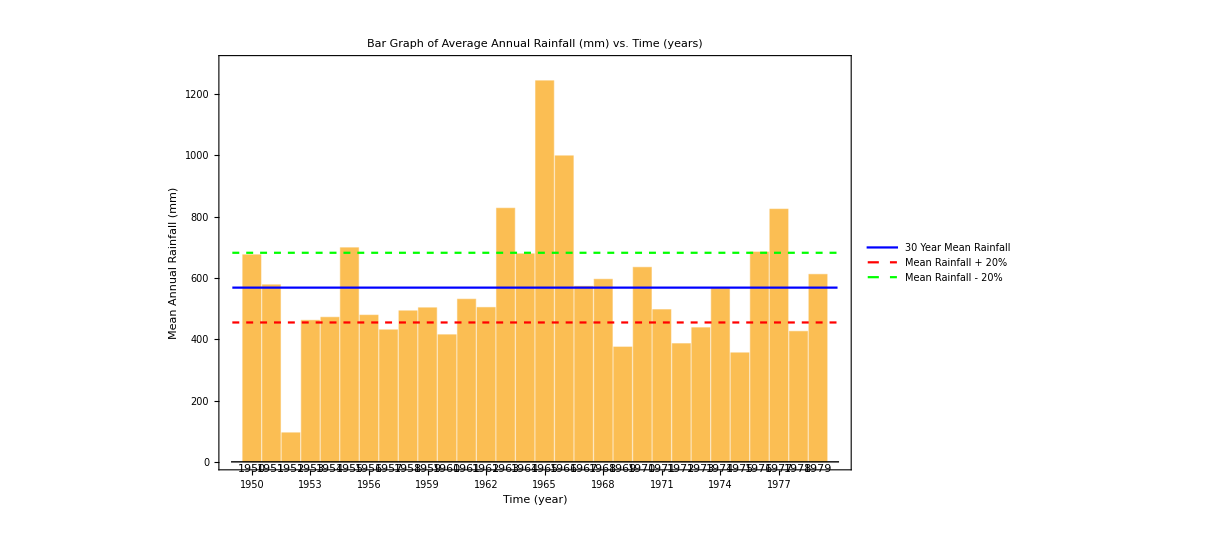

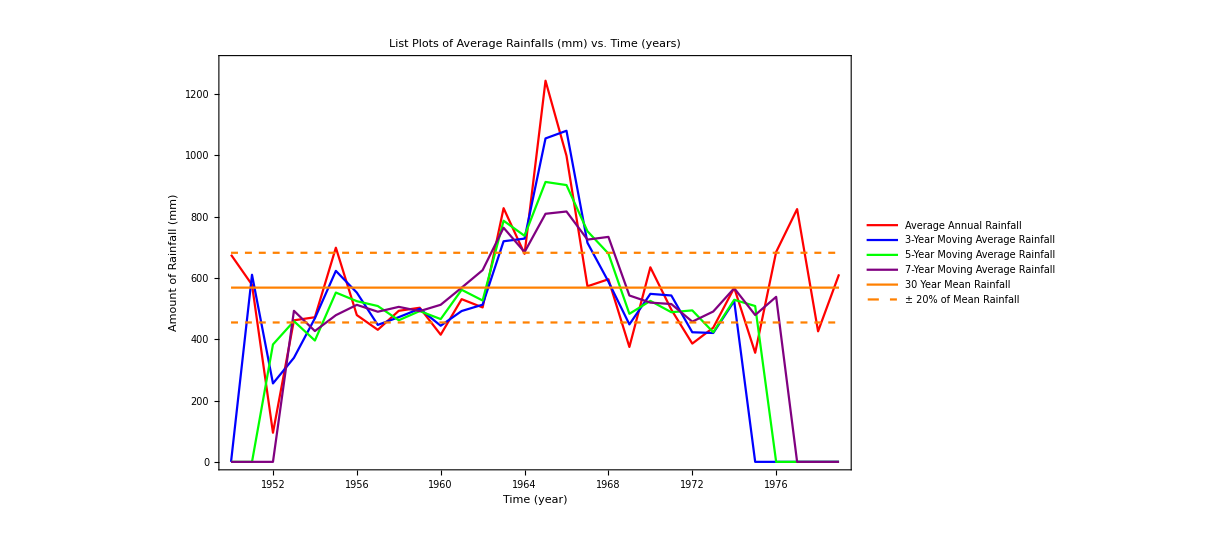

Year | Average Annual Rainfall (mm) | 3-Year Moving Average Rainfall (mm) | 5-Year Moving Average Rainfall (mm) | 7-Year Moving Average Rainfall (mm)
1950. | 676. | 0 | 0 | 0
1951. | 578. | 610.7 | 0 | 0
1952. | 95. | 256. | 383.2 | 0
1953. | 462. | 339.7 | 459.2 | 493.
1954. | 472. | 468.7 | 396. | 427.
1955. | 699. | 623.3 | 552.6 | 478.7
1956. | 479. | 552.3 | 524.4 | 512.4
1957. | 431. | 447. | 508.6 | 490.
1958. | 493. | 472.3 | 462.2 | 505.9
1959. | 503. | 499.7 | 492.2 | 492.
1960. | 415. | 444.3 | 466. | 512.7
1961. | 531. | 492.3 | 561.6 | 568.6
1962. | 504. | 513. | 526.6 | 625.7
1963. | 828. | 720. | 787. | 764.1
1964. | 679. | 728.7 | 737.8 | 684.7
1965. | 1244. | 1056. | 913.6 | 809.7
1966. | 999. | 1081. | 903.4 | 817.1
1967. | 573. | 715. | 752.8 | 725.4
1968. | 596. | 588.3 | 679.8 | 734.3
1969. | 375. | 448.7 | 483.2 | 543.
1970. | 635. | 548.3 | 525.4 | 519.7
1971. | 497. | 543. | 488.4 | 515.1
1972. | 386. | 423. | 494.4 | 457.6
1973. | 438. | 420.7 | 423. | 490.7
1974. | 568. | 524.7 | 529. | 566.7
1975. | 356. | 0 | 508.6 | 479.3
1976. | 685. | 0 | 0 | 538.6
1977. | 825. | 0 | 0 | 0
1978. | 426. | 0 | 0 | 0
1979. | 612. | 0 | 0 | 0

The Mean of Average Annual Rainfall = 568.667 mm

The Mean Rainfall + 20% = 682.4 mm

The Mean Rainfall - 20% = 454.933 mm

```mathematica
dataset=Import["C:\Users\swarupa\Downloads\RainfallData.txt","Table"];

dataset1=Table[{dataset[[a,1]],dataset[[a,2]],0,0,0},{a,2,31}];

bargraph=Show[{BarChart[dataset1[[All,2]],ChartLabels->{dataset1[[All, 1]]}],Plot[{Mean[dataset1[[All,2]]],0.8*Mean[dataset1[[All,2]]],1.2*Mean[dataset1[[All,2]]]},{x,0,31},PlotStyle->{{Blue,Thick},{Red,Thick,Dashed},{Green,Thick,Dashed}},PlotLegends->{"30 Year Mean Rainfall","Mean Rainfall + 20%","Mean Rainfall - 20%"}]},Frame->True,LabelStyle->{FontFamily->"Arial",FontSize->10,Directive[Bold,Black]},FrameLabel->{"Time (year)","Mean Annual Rainfall (mm)"},ImageSize->900,PlotRange->{0,1300},PlotLabel->"Bar Graph of Average Annual Rainfall (mm) vs. Time (years)"
]

For[i=2;j=3;k=4,i<30;j<29;k<28,i++;j++;k++,
dataset1[[i,3]]=Mean[{dataset1[[i-1,2]],dataset1[[i,2]],dataset[[i+1,2]]}];
dataset1[[j,4]]=Mean[{dataset1[[j-2,2]],dataset1[[j-1,2]],dataset1[[j,2]],dataset[[j+1,2]],dataset1[[j+2,2]]}];
dataset1[[k,5]]=Mean[{dataset1[[k-3,2]],dataset1[[k-2,2]],dataset1[[k-1,2]],dataset1[[k,2]],dataset[[k+1,2]],dataset1[[k+2,2]],dataset1[[k+3,2]]}];
]

movingaverageplot=Show[{ListLinePlot[dataset1[[All,{1,2}]],PlotStyle->{Red,Thick},PlotLegends->{"Average Annual Rainfall"}],ListLinePlot[dataset1[[All,{1,3}]],PlotStyle->{Blue,Thick},PlotLegends->{"3-Year Moving Average Rainfall"}],ListLinePlot[dataset1[[All,{1,4}]],PlotStyle->{Green,Thick},PlotLegends->{"5-Year Moving Average Rainfall"}],ListLinePlot[dataset1[[All,{1,5}]],PlotStyle->{Purple,Thick},PlotLegends->{"7-Year Moving Average Rainfall"}],Plot[{Mean[dataset1[[All,2]]],0.8*Mean[dataset1[[All,2]]],1.2*Mean[dataset1[[All,2]]]},{X,1950,1979},PlotStyle->{{Orange,Thick},{Orange,Thick,Dashed},{Orange,Thick,Dashed}},PlotLegends->{"30 Year Mean Rainfall","± 20% of Mean Rainfall"}]},Frame->True,LabelStyle->{FontFamily->"Arial",FontSize->10,Directive[Bold,Black]},FrameLabel->{"Time (year)","Amount of Rainfall (mm)"},ImageSize->900,PlotRange->{0,1300},PlotLabel->"List Plots of Average Rainfalls (mm) vs. Time (years)"
]

datasetP=Table[{0,0,0,0,0},{n,1,31}];
datasetP[[1]]={"Year","Average Annual Rainfall (mm)","3-Year Moving Average Rainfall (mm)","5-Year Moving Average Rainfall (mm)","7-Year Moving Average Rainfall (mm)"};
For[q=1,q<6,q++,
For[p=2,p<32,p++,
datasetP[[p,q]]=N[dataset1[[p-1,q]],4];
]
]
Print[TableForm[datasetP]]

StringForm["The Mean of Average Annual Rainfall = `` mm",N[Mean[dataset1[[All,2]]]]]
StringForm["The Mean Rainfall + 20% = `` mm",1.2*Mean[dataset1[[All,2]]]]
StringForm["The Mean Rainfall - 20% = `` mm",0.8*Mean[dataset1[[All,2]]]]
```